## Schrodinger’s Equation

## One Dimension

This is our twenty-third notebook. The goal for the remainder of the course will be to use Mathematica to help us solve and visualize the solutions to Schrodinger’s equation.

Let’s start with the harmonic oscillator.

### Potentials

Schrodinger’s equation is not written in terms of forces. It is written in terms of potentials. For a spring with spring constant k, the potential is:

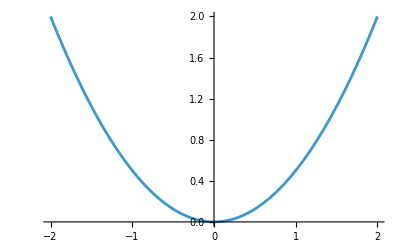

```mathematica
springPotential[x_]:=Module[{k=1},1/2 k x^2]
Plot[springPotential[x],{x,-2,2}]
```

You might completely reasonably ask what on Earth this potential has to do with the force F(x)=-kx. The deep relationship between potentials and forces is that the force is minus the derivative of the potential. Let’s have Mathematica compute the minus the derivative for us:

```mathematica
potential[x_]:=1/2 k x^2
-Derivative[1][potential][x]
```

-k x

Ok, the relationship is as claimed.

You are just going to have to accept that Schrodinger had the bright idea to use potentials as a way of introducing forces in quantum mechanics. If you have a couple of semesters of classical mechanics (one is not quite enough), this seems entirely reasonable, and even after one semester of classical mechanics it begins to seem reasonable.

### Schrodinger’s Equation

It is very common to use the letter ψ for the wave function. Here is the differential equation it satisfies:

```mathematica
-ℏ^2/(2m)Derivative[2][ψ][x]+1/2 k(x^2)[x]ψ[x]==energy ψ[x]//TraditionalForm
```

1/2 k x^2(x) ψ(x)-(ℏ^2 ψ''(x))/(2 m)==energy ψ(x)

### Units

I am about to set the very important constants (“hbar”, the particle mass, and the spring constant) all equal to one. You might ask why I didn’t set energy=1 as well. The reason is that that overconstrains the problem.

Imagine setting both the radius of a sphere equal to one, and the circumference of that same sphere equal to one. You’d quickly get garbage in whatever problem in which you did that. You can set the radius to one, in which case the circumference is 2π, or you can set the circumference to one, in which case the radius is 1/(2π), but you can’t set them both to one. What we are doing when we set a dimensionful quantity like the radius to one is actually choosing our units of length. We cannot then set some other unrelated or non-trivially related length to one.

When we set ℏ=k=m=1, we are choosing our units of length, time, and mass. We are then unable to also set energy=1, because the combination ℏ √(k/m) has units of energy.

Note that once again the combination √(k/m) has shown up, and just as we did when we first encountered this combination in the classical harmonic oscillator, we can give it the name ω, in which case the units of energy are ℏω.

### Boundary Conditions

Very strangely, in quantum mechanics particles can be where they have no business being classically. If a particle has energy E, then it has no business being further from the origin than the two solutions of E=1/2 k(x_±)^2. If this were also true in quantum mechanics, our boundary conditions would be to just set ψ(x_+)=ψ(x_-)=0.

In quantum mechanics, unless the potential gets infinitely high somewhere, the particle has some very small but nonzero chance of being far into the region it has no business being classically.

Let’s go a long, long ways into the “forbidden region” and demand that ψ(x) be zero there. Our left boundary condition will be:

```mathematica
longWays=3;
psi[-longWays]==0
```

psi[-3]==0

You know with equations with second derivatives you have to specify more than just one edge’s conditions. With the guitar string, we had to specify a boundary condition at the bridge and the nut. With the drumhead, we had to specify a boundary condition all around the edge. With this problem (for reasons you will soon see, but accept for the moment), the second boundary condition will be:

```mathematica
Derivative[1][psi][-longWays]==0.1
```

psi'[-3]==0.1

If your gut is saying this is arbitrary, your gut is right. Again, accept it for the moment.

### The Full Problem

Ok, we have the full problem, including boundary conditions now:

```mathematica
harmonicOscillatorProblem=Module[{ℏ=1,m=1,k=1},{-ℏ^2/(2m)Derivative[2][psi][x]+1/2 k x^2 psi[x]==energy psi[x],psi[-longWays]==0,Derivative[1][psi][-longWays]==0.1}];
harmonicOscillatorProblem // TraditionalForm
```

{1/2 x^2 psi(x)-(psi''(x))/2==energy psi(x),psi(-3)==0,psi'(-3)==0.1}

Note that time has not entered. This is another thing for me to discuss/explain, but because it hasn’t entered, you shouldn’t be bothered that we don’t have any initial conditions.

### Making Mathematica Solve the Problem

I am going to stick the entire problem into a Manipulate[] so that we can play with the one remaining variable, which is the energy:

```mathematica
Manipulate[Module[{psiSolution=NDSolveValue[harmonicOscillatorProblem/.energy->e,psi,{x,-longWays,longWays+1}]},Plot[psiSolution[x],{x,-longWays,longWays+1},PlotRange->{{-longWays,longWays+1},{-2,2}},PlotLabel->e]],{e,0,5}]
```

### Boundary Conditions Again

Boundary conditions are handled strangely in the Schrodinger’s equation. I mentioned that

```mathematica
Derivative[1][psi][-longWays]==0.1 // TraditionalForm
```

psi'(-3)==0.1

is arbitrary. The actual boundary condition we are looking for to complement

```mathematica
psi[-longWays]==0  (* longWays is 3 in our notebook *)
```

psi[-3]==0

is

```mathematica
psi[+longWays]==0
```

psi[3]==0

It turns out it is hard to make both of those things true. What you need to do is fiddle with the energy until ψ(3) is as close to 0 as you can make it. I chose longWays=3 because a larger longWays would require more precision than you can come close to achieving with the Manipulate[] control.

### Record the Energy Levels

Fiddle with the control in the Manipulate[]. You should be able to find five energy levels for which psi[+longWays] is pretty close to 0. Record them below, in ascending order:

"Level (n)" | "Energy (units of ℏω)"
0 | □
1 | □
2 | □
3 | □
4 | □

### Where Did Time Go?

In the real world, even the quantum-mechanical real world, things evolve with time. If we have time, I can roll up the screen and explain, using the separation of variables trick, where time disappeared to.

The equation that I have been calling “Schrodinger’s Equation” is, more precisely, known as the “Time-Independent Schrodinger Equation.” It is applicable to a system that has a definite energy, and solving it allows you to discover the allowable energies of the system. A general system, can have a mixture of energies. However, the mixture still only contains mixtures of the allowed energies.

If we are short of time, we can just proceed to the next notebook, where I will show you how to interpret the solutions ψ_n(x) and how combinations of solutions are added together to recover time-dependence.